```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=Delete[list,FirstPosition[list,element]](* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=Delete[list,Table[FirstPosition[list,i],{i,elementlist}]](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair ２つの枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアーとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)
```

### 渦電流の計算

```mathematica
Pin={{3.30204,9.09128},{3.30442,0.46863},{9.01646,6.24185},{9.31342,1.24199},{6.10577,2.96787},{5.75196,4.97666},{3.32525,5.95897},{1.84868,1.18248},{7.3017,7.41784},{4.80162,2.52861}}
(*Point input*)
```

{{3.30204,9.09128},{3.30442,0.46863},{9.01646,6.24185},{9.31342,1.24199},{6.10577,2.96787},{5.75196,4.97666},{3.32525,5.95897},{1.84868,1.18248},{7.3017,7.41784},{4.80162,2.52861}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

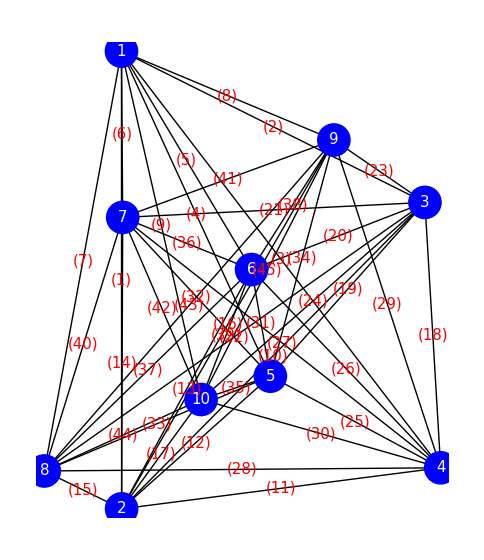

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

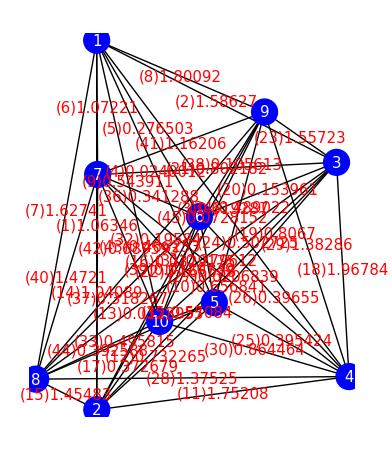

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### TSPの解

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

1→2 | 1→3 | 1→4 | 1→5 | 1→6 | 1→7 | 1→8 | 1→9 | 1→10 | 2→3
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

2→4 | 2→5 | 2→6 | 2→7 | 2→8 | 2→9 | 2→10 | 3→4 | 3→5 | 3→6
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

3→7 | 3→8 | 3→9 | 3→10 | 4→5 | 4→6 | 4→7 | 4→8 | 4→9 | 4→10
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

5→6 | 5→7 | 5→8 | 5→9 | 5→10 | 6→7 | 6→8 | 6→9 | 6→10 | 7→8
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

7→9 | 7→10 | 8→9 | 8→10 | 9→10
41 | 42 | 43 | 44 | 45

```mathematica
Curr
```

{1.06346,-1.58627,-0.619287,-0.0240012,-0.276503,1.07221,1.62741,-1.80092,0.543911,0.656841,1.75208,0.732265,0.0123955,-1.04089,-1.45483,0.0329175,0.372679,-1.96784,-0.8067,0.153961,0.802182,-0.165538,1.55723,-0.502725,-0.395424,0.39655,0.0206839,-1.37525,1.38286,-0.864464,0.279612,-0.19584,-0.495815,0.489022,-0.57084,0.341288,0.318267,-0.105613,0.0120739,1.4721,-1.16206,0.689593,-0.466253,0.392588,-0.0728152}

```mathematica
CurrCostSort=Reverse[Ordering[Abs[Curr]]](* 降順 *)
```

{18,8,11,7,2,23,40,15,29,28,41,6,1,14,30,19,21,12,42,10,3,35,9,24,33,34,43,26,25,44,17,36,37,31,5,32,22,20,38,45,16,4,27,13,39}

```mathematica
PDSort=Ordering[PD//N](* 昇順 *)
```

{35,15,31,23,17,36,39,38,6,44,20,25,42,12,32,41,8,19,34,33,30,5,40,18,13,26,37,14,45,24,21,11,2,29,9,4,28,27,16,7,10,43,1,22,3}

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{8.10813,4.02544,15.9647,280.601,17.319,2.92144,4.94113,2.40745,12.3767,12.3644,3.45792,5.12678,413.827,5.27469,1.11445,243.544,6.83321,2.54526,5.43047,22.7401,7.10342,53.,1.33523,11.1735,9.21159,13.0137,368.541,5.42808,4.69696,5.42725,7.29478,20.8531,9.31058,9.42262,2.41073,7.6709,17.1035,27.3788,217.498,3.39617,3.64491,5.41562,17.766,8.26641,75.4149}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{15,23,8,35,18,6,40,11,41,2,29,7,12,14,42,30,28,19,17,21,31,36,1,44,25,33,34,24,10,9,26,3,37,5,43,32,20,38,22,45,39,16,4,27,13}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{31.515,{1,9,3,4,2,8,10,5,6,7,1}}

-Graphics-

### 電流コストによるgreedyを用いた解法

```mathematica
CurrCostSort
```

{18,8,11,7,2,23,40,15,29,28,41,6,1,14,30,19,21,12,42,10,3,35,9,24,33,34,43,26,25,44,17,36,37,31,5,32,22,20,38,45,16,4,27,13,39}

{1,8,7,2,4,3,9,1}

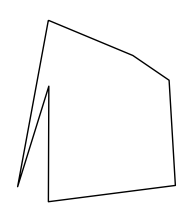

```mathematica
PartLoopByGreedyFromSort[CurrCostSort]
Graphics[Line[Pin[[%]]]]
```

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

### 電流コストによる新しいgreedyを用いた解法

```mathematica
CurrCostSort
```

{18,8,11,7,2,23,40,15,29,28,41,6,1,14,30,19,21,12,42,10,3,35,9,24,33,34,43,26,25,44,17,36,37,31,5,32,22,20,38,45,16,4,27,13,39}

{1,3,9,1}

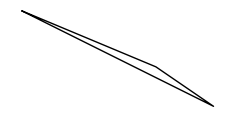

```mathematica
PartLoopByNewUndirectedGreedyFromSort[CurrCostSort]
Graphics[Line[Pin[[%]]]]
```

```mathematica
OutLoop1=EdgeSolution
```

{3→9,9→1,1→3}

```mathematica
RestEdgeSort[OutLoop1,Curr]
```

{15,28,14,30,35,33,25,32,39,13,27,31,37,36,17,44,26,42,12,40,11}

{4,8,5,10,4}

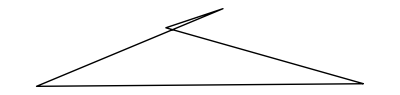

```mathematica
PartLoopByNewUndirectedGreedyFromSort[{15,28,14,30,35,33,25,32,39,13,27,31,37,36,17,44,26,42,12,40,11}]
Graphics[Line[Pin[[%]]]]
```

{4,7,5,4}

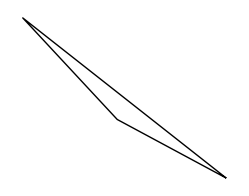

```mathematica
PartLoopByNewDirectedGreedyFromSort[{15,28,14,30,35,33,25,32,39,13,27,31,37,36,17,44,26,42,12,40,11}]
Graphics[Line[Pin[[%]]]]
```

```mathematica
(* 枝の向きを考慮した場合 *)
```

{1,3,4,2,8,1}

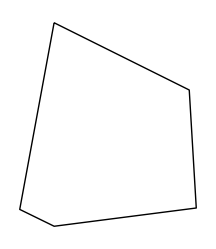

```mathematica
PartLoopByNewDirectedGreedyFromSort[CurrCostSort]
Graphics[Line[Pin[[%]]]]
```

```mathematica
OutLoop1={EdgeSolution}
```

{{4→3,3→1,1→8,8→2,2→4}}

```mathematica
OutLoop1=ContinuousInsertVertexLoop[OutLoop1[[1]]]
```

{{4→3,3→1,1→8,8→2,2→4},{4→3,1→8,8→2,2→4,3→9,9→1},{4→3,8→2,2→4,3→9,9→1,1→7,7→8}}

{1,9,3,4,2,8,7,1}

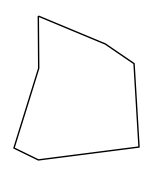

```mathematica
VertexSortFromLoopEdgeList[OutLoop1[[-1]]]
Graphics[Line[Pin[[%]]]]
```

```mathematica
RestEdgeSort[{4->3,8->2,2->4,3->9,9->1,1->7,7->8},Curr]
```

{35,39,31}

```mathematica
PartLoopByNewDirectedGreedyFromSort[{35,39,31}]
Graphics[Line[Pin[[%]]]]
```

{5,6,10,5}

-Graphics-

```mathematica
OutLoop2=EdgeSolution
```

{10→5,5→6,6→10}

```mathematica
OutLoop3=JoinPartLoop[OutLoop1[[-1]],OutLoop2]
```

{4→3,8→2,2→4,3→9,9→1,1→7,10→5,5→6,7→6,8→10}

{1,9,3,4,2,8,10,5,6,7,1}

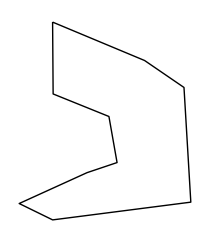

```mathematica
VertexSortFromLoopEdgeList[OutLoop3]
Graphics[Line[Pin[[%]]]]
```

### 距離と電流コストによるgreedyを用いた解法

```mathematica
PartLoopByGreedyFromSort[PDCurrCostSort]
Graphics[Line[Pin[[%]]]]
```

{1,7,8,2,4,3,9,1}

-Graphics-

```mathematica
OutLoop1=EdgeSolution
```

{2→8,8→7,7→1,1→9,9→3,3→4,4→2}

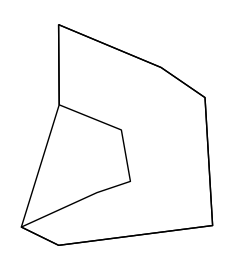

```mathematica
Show[-Graphics-,-Graphics-]
```

```mathematica
DelEdgeVertexList[Ruleg,{1,9,3,4,2,8,7,1}]
```

{5→6,5→10,6→10}

```mathematica
EdgeNumList[{5->6,5->10,6->10}]
```

{31,35,39}

```mathematica
PDCurrCost[[{31,35,39}]]
```

{7.29478,2.41073,217.498}

```mathematica
Ordering[PDCurrCost[[{31,35,39}]]]
```

{2,1,3}

```mathematica
EdgeNumList[{5->6,5->10,6->10}][[Ordering[PDCurrCost[[{31,35,39}]]]]]
```

{35,31,39}

```mathematica
RestEdgeSort[OutLoop1,PDCurrCost]
```

{35,31,39}

```mathematica
PartLoopByGreedyFromSort[{35,31,39}]
Graphics[Line[Pin[[%]]]]
```

{5,10,6,5}

-Graphics-

```mathematica
OutLoop2=EdgeRules[EdgeSolution]
```

{5→10,10→6,6→5}

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
SquareTourDiff[6->10,7->8]
```

-1.76227

```mathematica
SquareTourDiffList[OutLoop1,OutLoop2]
```

{{4.00197,3.74268,5.53658},{0.953509,-1.76227,0.195087},{5.9608,2.76489,3.70052},{5.62792,2.6617,3.02129},{6.41671,3.80345,3.15333},{2.68762,0.558048,0.0951962},{-1.24563,-0.977416,0.67381}}

```mathematica
Min[SquareTourDiffList[OutLoop1,OutLoop2]]
```

-1.76227

```mathematica
JoinPartLoop[OutLoop1,OutLoop2]
```

{2→8,7→1,1→9,9→3,3→4,4→2,5→10,6→5,8→10,7→6}

{1,7,6,5,10,8,2,4,3,9,1}

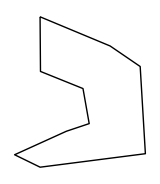

```mathematica
VertexSortFromLoopEdgeList[JoinPartLoop[OutLoop1,OutLoop2]]
Graphics[Line[Pin[[%]]]]
```

```mathematica
VertexSortFromLoopEdgeList[OutLoop2]
```

{5,10,6,5}

```mathematica
VertexSortFromLoopEdgeList[OutLoop1]
```

{1,7,8,2,4,3,9,1}

### 距離と電流コストによる新しいgreedyを用いた解法

```mathematica
PDCurrCostSort
```

{15,23,8,35,18,6,40,11,41,2,29,7,12,14,42,30,28,19,17,21,31,36,1,44,25,33,34,24,10,9,26,3,37,5,43,32,20,38,22,45,39,16,4,27,13}

{1,9,3,4,2,8,7,1}

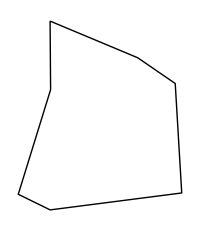

```mathematica
PartLoopByNewGreedyFromSort[PDCurrCostSort]
Graphics[Line[Pin[[%]]]]
```

```mathematica
OutLoop1=EdgeRules[EdgeSolution]
```

{8→2,2→4,4→3,3→9,9→1,1→7,7→8}

```mathematica
RestVertex[OutLoop1]
```

{5,6,10}

```mathematica
Table[Min[TriTourDiffList[OutLoop1,i]],{i,{5,6,10}}]
```

{1.33809,3.06195,1.1797}

```mathematica
Table[MinTriTourDiffPosition[OutLoop1,i],{i,{5,6,10}}]
```

{2,7,2}